```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab4

```mathematica
poly = Import["atan.txt","Table"][[1]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-5.95069×10^-11,5.64835×10^-9,-2.46864×10^-7,6.58669×10^-6,-0.00011993,0.00157794,-0.0154962,0.115689,-0.66253,2.91581,-9.81654,24.9982,-47.2285,64.1918,-59.7036,34.6696,-9.96789,-0.0935224,1.27522}

```mathematica
LagrangePolynom = ∑_(k=1)^(Length@poly) poly[[k]]*x^(Length@poly-k)
```

1.27522-0.0935224 x-9.96789 x^2+34.6696 x^3-59.7036 x^4+64.1918 x^5-47.2285 x^6+24.9982 x^7-9.81654 x^8+2.91581 x^9-0.66253 x^10+0.115689 x^11-0.0154962 x^12+0.00157794 x^13-0.00011993 x^14+6.58669×10^-6 x^15-2.46864×10^-7 x^16+5.64835×10^-9 x^17-5.95069×10^-11 x^18

```mathematica
LagrangePolynom /. x-> 6.79
```

-342.13

```mathematica
func /. x->6.79
```

0.637498

```mathematica
func = 1/ArcTan[1+10x^2]
```

1/ArcTan[1+10 x^2]

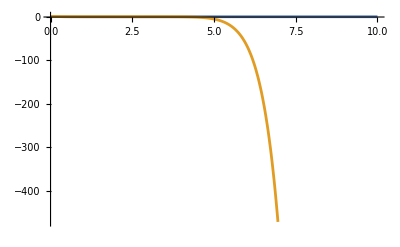

```mathematica
Plot[{func, LagrangePolynom},{x,0,10}]
```

```mathematica
f=((x-1)(x-2)(x-3))/((0-1)(0-2)(0-3)) + ((x)(x-2)(x-3))/((1-2)(1-3))E +((x)(x-1)(x-3))/((2)(2-1)(2-3))E^2 + ((x)(x-1)(x-2))/((3)(3-1)(3-2))E^3 // N //Expand
```

1.+1.93311 x-1.06036 x^2+0.845536 x^3

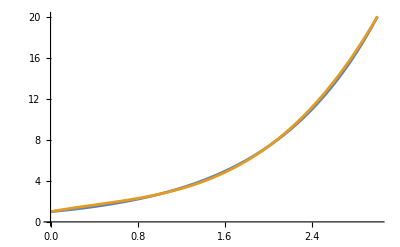

```mathematica
Plot[{E^x, LagrangePolynom},{x,0,3}]
```

```mathematica
((x-1)(x-2)(x-3))/((0-1)(0-2)(0-3)) +  ((x)(x-2)(x-3))/((1-2)(1-3))E + ((x)(x-1)(x-3))/((2)(2-1)(2-3))E^2 +((x)(x-1)(x-2))/((3)(3-1)(3-2))E^3// Expand // N
```

1.+1.93311 x-1.06036 x^2+0.845536 x^3

```mathematica
(x-1)(x-2)//Expand
```

2-3 x+x^2

```mathematica
0*x^36+0*x^35+0*x^34+0*x^33+0*x^32+0*x^31+0*x^30+0*x^29+0*x^28+0*x^27+0*x^26+0*x^25+0*x^24+0*x^23+0*x^22+0*x^21+0*x^20+0*x^19+-5.95069 * 10^-11*x^18+5.64835* 10^-9*x^17+-2.46864* 10^-7*x^16+6.58669* 10^-6*x^15+-0.00011993*x^14+0.00157794*x^13+-0.0154962*x^12+0.115689*x^11+-0.66253*x^10+2.91581*x^9+-9.81654*x^8+24.9982*x^7+-47.2285*x^6+64.1918*x^5+-59.7036*x^4+34.6696*x^3+-9.96789*x^2+-0.0935224*x+1.27522  /. x->6.79
```

-342.13

```mathematica
0.7*(-6*0.3+4) + (1-0.7)(-3*0.3 + 2)
```

1.87

```mathematica
0.7*0.3 + 0.7 + 0.3 +1
```

2.21

```mathematica
9.02501 - Exp[2.2]
```

-3.49943×10^-6

```mathematica
0.2^11 Exp[2]
```

1.51328×10^-7